```mathematica
amount = 10000;
Ns=192;   (* 48 *)
m=-0.8; (* -2.8 *)
sq = 3; (* 21 *)
(*page 36*)
```

```mathematica
normalDistribution[μ_, sqs_, numberOfValues_, n_]:= (
 σ = √sqs;
sequence = {};
For[i = 1, i≤ numberOfValues, i++,
ζ = √12/n*(∑_(i=1)^n RandomReal[] - n/2);
ξ = μ + σ * ζ ;
AppendTo[sequence, ξ];
];
sequence
)
```

```mathematica
customVariance[list_]:=N[Total[(#-Mean[list])^2&/@list]/(Length[list]-1)]
```

===1_TASK======================EXECUTION===============================

```mathematica
normal = normalDistribution[m, sq, amount, Ns];
```

```mathematica
Variance[normal]
```

2.98433

```mathematica
customVariance[normal]
```

3.0648

```mathematica
sq
```

3

```mathematica
Mean[normal]
```

-0.804599

```mathematica
m
```

-0.8

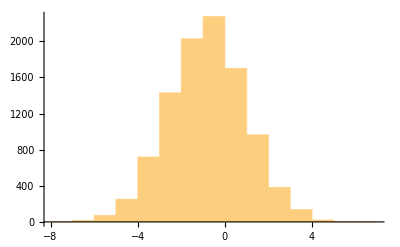

```mathematica
Histogram[normal]
```

=========================================================================

```mathematica
lambda = 0.25; (* 0.5 *)
(* 45 str - fisher *)
lmy = 5;
 mmy=3;
 a = 0;
 b = 1.5;
```

```mathematica
exponentialCore[λ_]:=(-Log[RandomReal[]])/λ;
```

```mathematica
exponentialDistribution[λ_, numberOfValues_]:= (
sequence = {};
For[i = 1, i≤ numberOfValues, i++,

AppendTo[sequence, exponentialCore[λ]];
];
sequence
)
```

```mathematica
logisticCore[μ_, k_]:=(
y = RandomReal[];
μ + k*Log[y/(1-y)]
);
```

```mathematica
logisticDistribution[μ_, k_, numberOfValues_]:= (
sequence = {};
For[i = 1, i≤ numberOfValues, i++,
AppendTo[sequence,logisticCore[μ, k]];
];
sequence
)
```

===2_TASK======================EXECUTION===============================

----------------Exponentials------------------------------------

```mathematica
exponential = exponentialDistribution[lambda, amount];
```

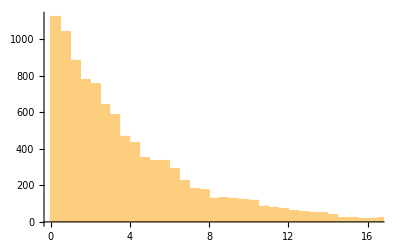

```mathematica
Histogram[exponential]
```

```mathematica
Variance[exponential]
```

16.0525

```mathematica
expVariance = 1/lambda^2
```

16.

```mathematica
Mean[exponential]
```

4.04717

```mathematica
expMean = 1/lambda
```

4.

----------------Logics-------------------------------------

```mathematica
logistic = logisticDistribution[a, b, amount]
```

{-1.23041,1.55785,4.68332,-0.0858064,-1.46983,0.272535,-1.21817,-1.91072,2.028,6.24359,-1.88966,0.499994,-0.505625,1.94747,-1.46696,9970,1.3776,1.03487,0.132313,-0.123596,0.106184,3.34634,-3.79864,-0.00106533,0.359619,0.34238,0.235037,-0.0427302,0.277613,-6.19484,-1.80835}
 |  |  |  |

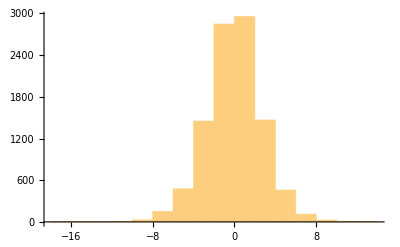

```mathematica
Histogram[logistic]
```

```mathematica
Variance[logistic]
```

7.30351

```mathematica
logisticVariance =Pi^2/3*b^2
```

7.4022

```mathematica
Mean[logistic]
```

-0.0150823

```mathematica
logisticMean= a
```

0